```mathematica
SetDirectory[NotebookDirectory[]];
```

# Model 003

## Alternative names: ‘Modified basic model with coupled metallicity’

## Constants

```mathematica
τS=26/10; (*[Gyr]*)
Rh=19/10;(*[cm^3 Gyr^-1]*)
σνB=8158;(*[cm^3 Gyr^-1]*)
Zsun=134/10000;
Zeff=10^-3*Zsun;
Zsn=9/100;
ηion=95529/100;
ηdiss=38093/100;
R=18/100;
```

## System of equations

```mathematica
(*
	Ionized gas fraction:        i(t) / g -> y[1]
	Atomic gas fraction:         a(t) / g -> y[2]
	Molecular gas fraction:      m(t) / g -> y[3]
	Metal fraction:              z(t) / g -> y[4]
	Stellar fraction:            s(t) / g -> y[5]	
	where g = i(t) + a(t) + m(t)
     
	Each equation has Gyr^(-1) [years^(-9)] as its units on the LHS and RHS
*)
```

```mathematica
vars={i[t],a[t],m[t],z[t],s[t]};
Z=z[t];
ψ=m[t]/τS;
τR=1/(n*σνB);
τC=Zsun/(2*n*Rh*(Z+Zeff));
recombination=i[t]/τR;
cloudFormation=a[t]/τC;
equ= {
i'[t]==-recombination+ηion*ψ,
a'[t]==-cloudFormation+recombination+(ηdiss-ηion)*ψ,
m'[t]==cloudFormation-(1+ηdiss)*ψ,
z'[t]==(Zsn*R-Z)*ψ,
s'[t]==ψ
};
```

## Solving the system

### Integration span

```mathematica
Tstart=0; (*[Gyr]*)
Tend=1; (*[Gyr]*)
```

### Initial conditions

```mathematica
i0=6/10;
a0=2/10;
m0=2/10;
z0=10^-4;
s0=0;
initCond={i0,a0,m0,z0,s0};
```

### Parameters

```mathematica
params = Normal[AssociationThread[{n},{10^-3}]];(*{n [cm^-3]}*)
```

### Integration

```mathematica
system = Join[equ,
{
i[Tstart]==i0,
a[Tstart]==a0,
m[Tstart]==m0,
z[Tstart]==z0,
s[Tstart]==s0
}]/.params;
solutions=vars/.NDSolve[system,vars,{t,Tstart,Tend}][[1]];
```

### Save data in file

```mathematica
LogTstart=-5;
LogTend=Log10[Tend]; 
points=10^4;
times=N[Table[10^i,{i,LogTstart,LogTend,(LogTend-LogTstart)/points}],8];
```

```mathematica
denseData=Table[{N[t,6],solutions[[1]],solutions[[2]],solutions[[3]],solutions[[4]], solutions[[5]]},{t,times}];
output=Prepend[denseData,{"t    i(t)    a(t)    m(t)    z(t)    s(t)"}];
```

```mathematica
Export["plots/mathematica.dat",output,"Table"];
```

## Plots

```mathematica
igf=Table[{denseData[[i,1]],denseData[[i,2]]},{i,2,Length[denseData]}];
agf=Table[{denseData[[i,1]],denseData[[i,3]]},{i,2,Length[denseData]}];
mgf=Table[{denseData[[i,1]],denseData[[i,4]]},{i,2,Length[denseData]}];
metals=Table[{denseData[[i,1]],denseData[[i,5]]},{i,2,Length[denseData]}];
stars=Table[{denseData[[i,1]],denseData[[i,6]]},{i,2,Length[denseData]}];
```

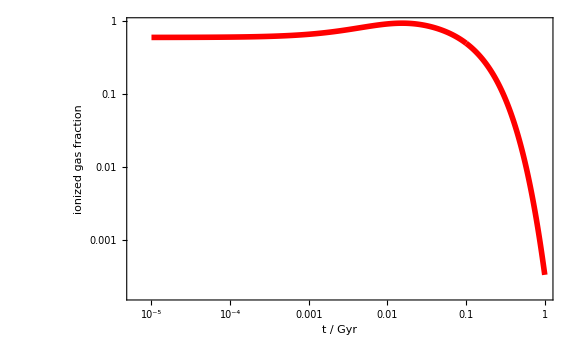

```mathematica
ListLogLogPlot[
igf,
Joined->True,
PlotStyle->{Thickness[0.007],Red},
Frame->True,
FrameLabel->{Style["t / Gyr",16],Style["ionized gas fraction",16] },
FrameStyle->Directive[Black,14],
ImageSize->Large
]
```

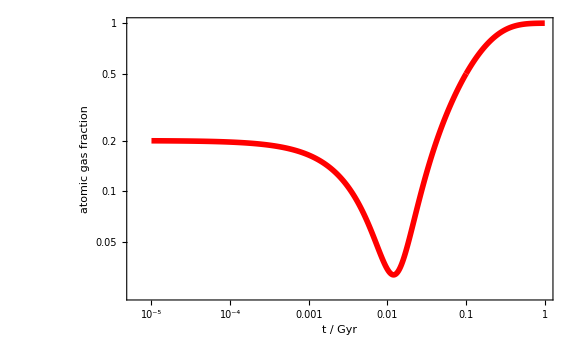

```mathematica
ListLogLogPlot[
agf,
Joined->True,
PlotStyle->{Thickness[0.007],Red},
Frame->True,
FrameLabel->{Style["t / Gyr",16],Style["atomic gas fraction",16] },
FrameStyle->Directive[Black,14],
ImageSize->Large
]
```

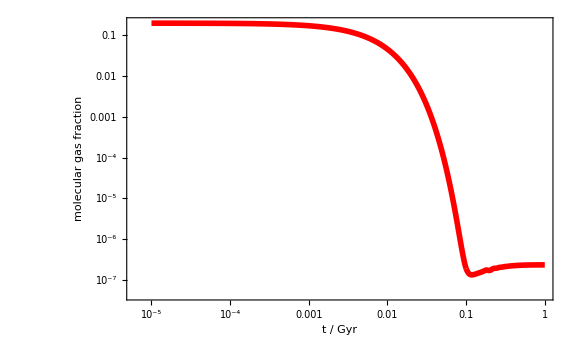

```mathematica
ListLogLogPlot[
mgf,
Joined->True,
PlotStyle->{Thickness[0.007],Red},
Frame->True,
FrameLabel->{Style["t / Gyr",16],Style["molecular gas fraction",16] },
FrameStyle->Directive[Black,14],
ImageSize->Large
]
```

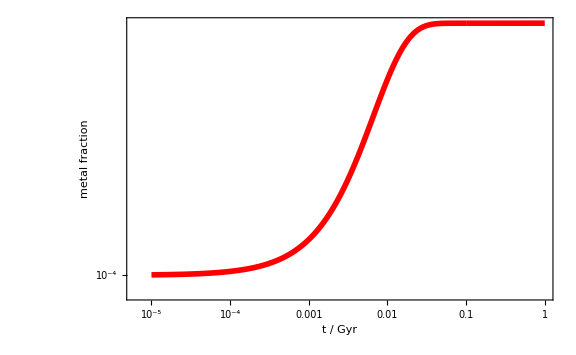

```mathematica
ListLogLogPlot[
metals,
Joined->True,
PlotStyle->{Thickness[0.007],Red},
Frame->True,
FrameLabel->{Style["t / Gyr",16],Style["metal fraction",16] },
FrameStyle->Directive[Black,14],
ImageSize->Large
]
```

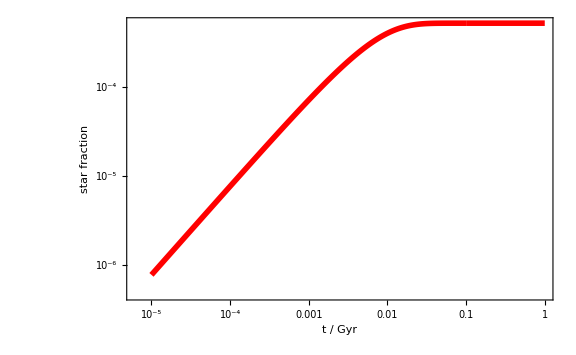

```mathematica
ListLogLogPlot[
stars,
Joined->True,
PlotStyle->{Thickness[0.007],Red},
Frame->True,
FrameLabel->{Style["t / Gyr",16],Style["stellar fraction",16] },
FrameStyle->Directive[Black,14],
ImageSize->Large
]
```

## Jacobian matrix

### Jacobian evaluated at the initial condition

```mathematica
iniCondAss=Normal[AssociationThread[vars,initCond]];
jacobian=D[Map[(#[[2]])&,equ],{vars}]/.Join[iniCondAss,params];
ScientificForm[MatrixForm[N[jacobian,3]]]
```

(-8.1580 | 0 | 3.67419×10^2 | 0 | 0
8.1580 | -3.2158×10^-5 | -2.20908×10^2 | -5.6716×10^-2 | 0
0 | 3.2158×10^-5 | -1.46896×10^2 | 5.6716×10^-2 | 0
0 | 0 | 6.19231×10^-3 | -7.69231×10^-2 | 0
0 | 0 | 3.84615×10^-1 | 0 | 0)

### Jacobian and time derivatives in C syntax

```mathematica
cStringAss=Join[
Normal[AssociationThread[
Map[ToString@*CForm,vars],
Table[ToString[y[i]],{i,0,Length[vars]-1}]
]],
{"Power(2.71828182845905,"->"exp(","Power"->"pow","Sqrt"->"sqrt"}
];
```

```mathematica
CJacobian=Map[ToString@*CForm,N[D[Map[(#[[2]])&,equ],{vars}],10],{2}];
CJacobian=Map[StringReplace[#,cStringAss]&,CJacobian];
```

```mathematica
ExpTimeJacobian =ReplaceAll[Map[(#[[2]])&,equ],Normal[AssociationMap[Head,vars]]];
CTimeDeriv=Map[ToString@*CForm,N[D[ExpTimeJacobian,t],10]];
CTimeDeriv=Map[StringReplace[#,cStringAss]&,CTimeDeriv];
```

### Jacobian for Boost odeint

```mathematica
jacobi=
StringJoin[
Flatten[
Table[
Join[{"\n"},
Table[
ToString[
StringForm["\t\tJ(``,``) = ``;\n",k-1,j-1,CJacobian[[k,j]]
]],{j,1,Length[vars]}]],{k,1,Length[vars]}]]];
timeDeriv=
Flatten[
Table[
ToString[
StringForm["\t\tdfdt[``] = ``;\n",j-1,CTimeDeriv[[j]]
]],{j,1,Length[vars]}]];
head="/*******************************************************************************************
* Jacobian for the model 003 calculated with Wolfram Language
* and adapted for its use with the Boost odeint library.
*******************************************************************************************/

struct jacobian
{
    template <class State, class Matrix>
    void operator()(const State &y, Matrix &J, const double &t, State &dfdt)
    {
        (void)(t);\n";
tail="    }
};";
Export["jacobian_boost.txt",StringJoin[head,jacobi,"\n",timeDeriv,tail]];
```

### Jacobian for GSL

```mathematica
jacobi=
StringJoin[
Flatten[
Table[
Join[{"\n"},
Table[
ToString[
StringForm["\tgsl_matrix_set(m, ``, ``, ``);\n",k-1,j-1,CJacobian[[k,j]]
]],{j,1,Length[vars]}]],{k,1,Length[vars]}]]];
timeDeriv=
Flatten[
Table[
ToString[
StringForm["\tdfdt[``] = ``;\n",j-1,CTimeDeriv[[j]]
]],{j,1,Length[vars]}]];
head=StringJoin["/*******************************************************************************************
* Jacobian for the model 003 calculated with Wolfram Language 
* and adapted for its use with the GSL library.
*******************************************************************************************/

int jacobian(double t, const double y[], double *dfdy, double dfdt[], void *params)
{
	(void)(t);

	double n = *(double *)params;\n\n",
ToString[
StringForm[
"\tgsl_matrix_view dfdy_mat = gsl_matrix_view_array(dfdy, ``, ``);\n",Length[vars],Length[vars]]],
	"\tgsl_matrix * m = &dfdy_mat.matrix;\n"];
tail="
	return GSL_SUCCESS;
};";
Export["jacobian_gsl.txt",StringJoin[head,jacobi,"\n",timeDeriv,tail]];
```

## Stiffness coefficient

```mathematica
StiffCoeff[equ_, vars_, y0_,params_]:=
Module[
{jacobian, association,Njacobian,eigenval},
jacobian=D[Map[(#[[2]])&,equ],{vars}];
association=Normal[AssociationThread[vars,y0]];
Njacobian=N[jacobian/.Join[association,params],16];
eigenval=DeleteCases[RealAbs[Re[Chop[Eigenvalues[Njacobian],10^-16]]],x_/;x==0];
Return[Max[eigenval]/Min[eigenval]];
]
```

```mathematica
StiffCoeff[equ,vars,initCond,params]
```

1.74459×10^9